```mathematica
(* chemistry *)
fv[v_,k_]:=-k v;

(* spacing *)
h[Subscript[ρ_, i_][t_]]:=Subscript[ρ, i+1][t]-Subscript[ρ, i] [t] (* ρ here is nondimensionalized r in the Boissonade paper *) 

(* structural response *)
ϕ[n_,ϕic_,Subscript[ρ_, i_][t_]]:=
Which[
1<i<n,ϕic/(n-1)2/(h[Subscript[ρ, i][t]]+h[Subscript[ρ, i-1][t]]),
i==1,ϕic/(n-1)2/h[Subscript[ρ, 1][t]], (* (ϵ+1) is in the denominator, but we approximate it to 1 because ϵ is very small *)
i==n,ϕic/(n-1)2/h[Subscript[ρ, n-1][t]]  (* (ϵ+1) is in the denominator, but we approximate it to 1 because ϵ is very small *)
] (* This definition of ϕ accounts for Subscript[ϕ, i] to Subscript[ϕ, n] *)
G[n_,D0_,KD_,{ϕ0_,ϕic_},Subscript[ρ_, i_][t_]]:=1/(D0 Exp[-KD √ϕ[n,ϕic,Subscript[ρ, i][t]]]) (* The R T in Δμ and G[ϕ] cancel each other out *)
χ[v_,vstar_,χmin_,χmax_,α_]:=(χmin+χmax)/2+(χmax-χmin)/2 Tanh[α(v-vstar)]  
Δμmix[n_,Subscript[ρ_, i_][t_],Subscript[v_, i_][t_],Subscript[vstar_, i_][t_],ϕic_,χmin_,χmax_,α_]:=(ϕ[n,ϕic,Subscript[ρ, i][t]]+Log[1-ϕ[n,ϕic,Subscript[ρ, i][t]]]+χ[Subscript[v, i][t],Subscript[vstar, i][t],χmin,χmax,α] (ϕ[n,ϕic,Subscript[ρ, i][t]])^2)
Δμel[n_,Subscript[ρ_, i_][t_],{ϕ0_,ϕic_},Knet_]:=Knet ((ϕ[n,ϕic,Subscript[ρ, i][t]]/ϕ0)^(1/3)-1/2(ϕ[n,ϕic,Subscript[ρ, i][t]]/ϕ0))
Δμ[n_,Subscript[ρ_, i_][t_],Subscript[v_, i_][t_],Subscript[vstar_, i_][t_],{ϕ0_,ϕic_},χmin_,χmax_,α_,Knet_]:=Δμmix[n,Subscript[ρ, i][t],Subscript[v, i][t],Subscript[vstar, i][t],ϕic,χmin,χmax,α]+Δμel[n,Subscript[ρ, i][t],{ϕ0,ϕic},Knet]
Δμbcfun[ϕeqvbc_,ϕ0_,vbc_,vstarbc_,χmin_,χmax_,α_,Knet_]:=(ϕeqvbc+Log[1-ϕeqvbc]+χ[vbc,vstarbc,χmin,χmax,α] ϕeqvbc^2)+Knet ((ϕeqvbc/ϕ0)^(1/3)-1/2(ϕeqvbc/ϕ0))
```

```mathematica
(* functions of n *) (* This whole section is to define functions V and Ρ and VSTAR which are Subscript[v, 1] to Subscript[v, n] and Subscript[ρ, 1] to Subscript[ρ, n] and Subscript[vstar, 1] to Subscript[vstar, n] *)
V[t_,n_]:=Table[Subscript[v, i][t],{i,1,n}];
Ρ[t_,n_]:=Table[Subscript[ρ, i][t],{i,1,n}];
VSTAR[t_,n_]:=Table[Subscript[vstar, i][t],{i,1,n}];


middleV[t_,n_,rmax_,{k_,Dv_}]:=Table[fv[Subscript[v, i][t],k]+Dv/rmax^2(2(Subscript[v, i+1][t]+h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]] Subscript[v, i-1][t]-(1+h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]])Subscript[v, i][t]))/(h[Subscript[ρ, i][t]]h[Subscript[ρ, i-1][t]](1+h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]]))(*(2(Subscript[v, i+1]+Subscript[h, i]/Subscript[h, i-1] Subscript[v, i-1]-(1+Subscript[h, i]/Subscript[h, i-1])Subscript[v, i]))/(Subscript[h, i] Subscript[h, i-1](1+Subscript[h, i]/Subscript[h, i-1]))*),{i,2,n-1}]; (* middleV is the middle section of the list of Subscript[v, i] to Subscript[v, n] that does not include the endpoints, Subscript[v, i] and Subscript[v, n] *)
rhseqnsV[t_,n_,rmax_,{k_,Dv_},vbc_,ϵ_]:=                   (* This has Dirichlet BC *) (* rhseqnsV is the full list Subscript[v, i] to Subscript[v, n]. It is called rhseqnsV because it is the right hand side of eqnsV. *)
Join[
{fv[Subscript[v, 1][t],k]+Dv/rmax^2(2(Subscript[v, 2][t]+1/ϵ vbc-(1+1/ϵ)Subscript[v, 1][t]))/(ϵ h[Subscript[ρ, 1][t]]^2(1+1/ϵ))(*(2(vbc-Subscript[v, 1]))/(ϵ h[Subscript[ρ, 1]]^2)*)}
,middleV[t,n,rmax,{k,Dv}]
,{fv[Subscript[v, n][t],k]+Dv/rmax^2(2(vbc+ϵ Subscript[v, n-1][t]-(1+ϵ)Subscript[v, n][t]))/(ϵ h[Subscript[ρ, n-1][t]]^2(1+ϵ))(*(2(vbc-Subscript[v, n]))/(ϵ h[Subscript[ρ, n-1]]^2)*)}
];
eqnsV[t_,n_,rmax_,{k_,Dv_},vbc_,ϵ_]:=Thread[                            (* eqnsV is the list from D[Subscript[V, i][t]]=Subscript[v, i][variables] to D[Subscript[V, n][t]]=Subscript[v, n][variables] *)
D[V[t,n],t]==rhseqnsV[t,n,rmax,{k,Dv},vbc,ϵ]
]

(* eqnsΡ follows the same method as eqnsV *)
middleΡ[t_,n_,rmax_,{ϕ0_,ϕic_},D0_,KD_,χmin_,χmax_,α_,Knet_]:=Table[(1-ϕ[n,ϕic,Subscript[ρ, i][t]])/(ϕ[n,ϕic,Subscript[ρ, i][t]]G[n,D0,KD,{ϕ0,ϕic},Subscript[ρ, i][t]])1/rmax^2 
1/(h[Subscript[ρ, i][t]](1+h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]]))(Δμ[n,Subscript[ρ, i+1][t],Subscript[v, i+1][t],Subscript[vstar, i+1][t],{ϕ0,ϕic},χmin,χmax,α,Knet]-(h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]])^2 Δμ[n,Subscript[ρ, i-1][t],Subscript[v, i-1][t],Subscript[vstar, i-1][t],{ϕ0,ϕic},χmin,χmax,α,Knet]-(1-(h[Subscript[ρ, i][t]]/h[Subscript[ρ, i-1][t]])^2)Δμ[n,Subscript[ρ, i][t],Subscript[v, i][t],Subscript[vstar, i][t],{ϕ0,ϕic},χmin,χmax,α,Knet])
,{i,2,n-1}]
rhseqnsΡ[t_,n_,rmax_,{ϕ0_,ϕic_},D0_,KD_,χmin_,χmax_,α_,Knet_,ϵ_,Δμbc_]:= 
Join[
{(1-ϕ[n,ϕic,Subscript[ρ, 1][t]])/(ϕ[n,ϕic,Subscript[ρ, 1][t]]G[n,D0,KD,{ϕ0,ϕic},Subscript[ρ, 1][t]])1/rmax^2 
1/(h[Subscript[ρ, 1][t]](1+1/ϵ))(Δμ[n,Subscript[ρ, 2][t],Subscript[v, 2][t],Subscript[vstar, 2][t],{ϕ0,ϕic},χmin,χmax,α,Knet]-(1/ϵ)^2 Δμbc-(1-(1/ϵ)^2)Δμ[n,Subscript[ρ, 1][t],Subscript[v, 1][t],Subscript[vstar, 1][t],{ϕ0,ϕic},χmin,χmax,α,Knet])}
,middleΡ[t,n,rmax,{ϕ0,ϕic},D0,KD,χmin,χmax,α,Knet]
,{(1-ϕ[n,ϕic,Subscript[ρ, n][t]])/(ϕ[n,ϕic,Subscript[ρ, n][t]]G[n,D0,KD,{ϕ0,ϕic},Subscript[ρ, n][t]])1/rmax^2 
1/(ϵ h[Subscript[ρ, n-1][t]](1+ϵ))(Δμbc-(ϵ)^2 Δμ[n,Subscript[ρ, n-1][t],Subscript[v, n-1][t],Subscript[vstar, n-1][t],{ϕ0,ϕic},χmin,χmax,α,Knet]-(1-(ϵ)^2)Δμ[n,Subscript[ρ, n][t],Subscript[v, n][t],Subscript[vstar, n][t],{ϕ0,ϕic},χmin,χmax,α,Knet])}
];
eqnsΡ[t_,n_,rmax_,{ϕ0_,ϕic_},D0_,KD_,χmin_,χmax_,α_,Knet_,ϵ_,Δμbc_]:=Thread[
D[Ρ[t,n],t]==rhseqnsΡ[t,n,rmax,{ϕ0,ϕic},D0,KD,χmin,χmax,α,Knet,ϵ,Δμbc]
]

(* eqnsVSTAR follows the same method as eqnsV *)


middleVSTAR[t_,n_,{h0_,ampl_,s_,r1_,r3_},tsvs_]:=Table[1/tsvs(-(Subscript[v, i][t]-h0)ampl+r1 (Subscript[vstar, i][t]-s)-r3(Subscript[vstar, i][t]-s)^3),{i,2,n-1}];
rhseqnsVSTAR[t_,n_,{h0_,ampl_,s_,r1_,r3_},tsvs_]:=                 
Join[
{1/tsvs(-(Subscript[v, 1][t]-h0)ampl+r1 (Subscript[vstar, 1][t]-s)-r3(Subscript[vstar, 1][t]-s)^3)}
,middleVSTAR[t,n,{h0,ampl,s,r1,r3},tsvs]
,{1/tsvs(-(Subscript[v, n][t]-h0)ampl+r1 (Subscript[vstar, n][t]-s)-r3(Subscript[vstar, n][t]-s)^3)}
];
eqnsVSTAR[t_,n_,{h0_,ampl_,s_,r1_,r3_},tsvs_]:=Thread[
D[VSTAR[t,n],t]==rhseqnsVSTAR[t,n,{h0,ampl,s,r1,r3},tsvs]
]

 
(* The initial conditions for each v and ρ and dtvstar equation from i to n are set below. *)
initcV[n_,v0_]:=Thread[V[0,n]==Table[v0,{i,1,n}]]
initcΡ[n_]:=Thread[Ρ[0,n]==Table[(i-1)/(n-1) ,{i,1,n}]] (* This is derived in your notebook. *)
initVSTAR[n_,vstar0_]:=Thread[VSTAR[0,n]==Table[vstar0,{i,1,n}]]
```

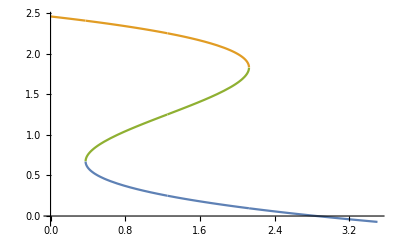

{h0→1.25,ampl→4.4,s→1.25,r1→10,r3→10}

```mathematica
vstarss[v_,{h0_,ampl_,s_,r1_,r3_}]:=Evaluate[vstar/.Simplify@Solve[-(v-h0)ampl+r1 (vstar-s)-r3(vstar-s)^3==0,vstar]]
vstarparam={1.25,4.4,1.25,10,10};
vstarparamsublist=Thread[{h0,ampl,s,r1,r3}->vstarparam];
Plot[Evaluate@(vstarss[v,vstarparam]),{v,0,3.5}]
```

```mathematica
(* Dynamic Plotting *)
Manipulate[
(* collapsed state is v=0. This state is taken as the reference state for ϕ0 *)
ϕ0=ϕ00/.Flatten@FindInstance[(ϕ00+Log[1-(ϕ00)]+χ[0,(Re[vstarss[0,vstarparam]]⟦2⟧),χmin,χmax,α] ϕ00^2)+Knet/2==0,ϕ00,Reals]; (* The above is solving for the steady state of ϕ0 in this equation. *)

Vr0coll=ϕ0^-1; (* The definition of Vr is Vr = ϕ^-1. Vr0coll is Vr where ϕ=ϕ0 *)
ϕeq=ϕbc/.FindInstance[(ϕbc+Log[1-(ϕbc)]+χ[vbc,(Re[vstarss[vbc,vstarparam]]⟦1⟧),χmin,χmax,α] ϕbc^2)+Knet ((ϕbc/ϕ0)^(1/3)-1/2(ϕbc/ϕ0))==0,ϕbc,Reals,2][[2]];
(* The above is solving for the steady state of ϕbc in this equation. *)

Vr0eq=ϕeq^-1;  (* The definition of Vr is Vr = ϕ^-1. Vr0coll is Vr where ϕ=ϕeq *)
ϕiceq=ϕicc/.Flatten@FindInstance[(ϕicc+Log[1-(ϕicc)]+χ[vic,(Re[vstarss[vic,vstarparam]]⟦If[expansion,2,1]⟧),χmin,χmax,α] ϕicc^2)+Knet ((ϕicc/ϕ0)^(1/3)-1/2(ϕicc/ϕ0))==0,ϕicc,Reals,2][[2]];
(* The above is solving for the steady state of ϕbc in this equation. *)

ϕic=If[iceq,ϕiceq,ϕ0]; (* If ϕic = iceq, then ϕic=ϕiceq. If ϕic does not = iceq, then ϕic=ϕ0. This is because it needs to rescale the space domain. *)
Vrss=Vr/.Flatten@FindInstance[(ϕ0/Vr(*1/(ϕ0 Vr)*)+Log[1-(ϕ0/Vr(*1/(ϕ0 Vr)*))]+χ[vbc/(1+Vr^2/(10^LOGDv/(2ϵ2var 10^LOGk))),(Re[vstarss[vbc/(1+Vr^2/(10^LOGDv/(2ϵ2var 10^LOGk))),vstarparam]]⟦1⟧),χmin,χmax,α] (ϕ0/Vr(*1/(ϕ0 Vr)*))^2)+Knet ((1/Vr)^(1/3)-1/2(1/Vr))==0,Vr,Reals];

(* The above is solving for the steady state of Vr in this equation. *)
vss=vbc/(1+Vrss^2/(10^LOGDv/(2ϵ2var 10^LOGk)));  

Module[{Δμbccoll,linescoll,Δμbc,lines,sim2var,ϕeqvbc},

Δμbccoll=Δμbcfun[ϕ0,ϕ0,0,(Re[vstarss[0,vstarparam]]⟦2⟧),χmin,χmax,α,Knet]; (* Here, ϕeqvbc = ϕ0 and vbc = 0 *)
linescoll=NDSolve[
{
eqnsV[t,n,rmax,{10^LOGk,10^LOGDv},0,ϵ]
,eqnsΡ[t,n,rmax,{ϕ0,ϕic},10^LOGD0,KD,χmin,χmax,α,Knet,ϵ,Δμbccoll]
,eqnsVSTAR[t,n,vstarparam,10^LOGtsvs]
,initcV[n,0]
,initcΡ[n]
,initVSTAR[n,(Re[vstarss[0,vstarparam]]⟦2⟧)]
}
,V[t,n]~Join~Ρ[t,n]~Join~VSTAR[t,n]
,{t,0,tmax}
];

(* "linescoll" is the same as "lines" except in "linescoll", vic = vbc = 0 *)

Δμbc=Δμbcfun[ϕeq,ϕ0,vbc,(Re[vstarss[vbc,vstarparam]]⟦1⟧),χmin,χmax,α,Knet];
lines=NDSolve[
{
eqnsV[t,n,rmax,{10^LOGk,10^LOGDv},vbc,ϵ]
,eqnsΡ[t,n,rmax,{ϕ0,ϕic},10^LOGD0,KD,χmin,χmax,α,Knet,ϵ,Δμbc]
,eqnsVSTAR[t,n,vstarparam,10^LOGtsvs]
,initcV[n,vic]
,initcΡ[n]
,initVSTAR[n,(Re[vstarss[vic,vstarparam]]⟦If[expansion,2,1]⟧)]
}
,V[t,n]~Join~Ρ[t,n]~Join~VSTAR[t,n]
,{t,0,tmax}
];
sim2var=NDSolve[
{
D[v[t],t]==-10^LOGk v[t]+10^LOGDv/(2 ϵ2var Vr[t]^2)(vbc-v[t])
,D[Vr[t],t]==10^LOGD0/(2 ϵ2var)Exp[-KD √(ϕ0/Vr[t]^2)](1/Vr[t]-1/ϕ0)(ϕ0/Vr[t]+Log[1-ϕ0/Vr[t]]+χ[v[t],vstar[t],χmin,χmax,α](ϕ0/Vr[t])^2+Knet(Vr[t]^(-1/3)-1/(2Vr[t])))
,D[vstar[t],t]==1/10^LOGtsvs((-(v[t]-h0)ampl+r1 (vstar[t]-s)-r3(vstar[t]-s)^3)/.vstarparamsublist)
,v[0]==vic
,vstar[0]==(Re[vstarss[vic,vstarparam]]⟦If[expansion,2,1]⟧)
,Vr[0]==1 (* B/c ϕ[0] = ϕ0 so, Vr[0] = ϕ0/ϕ0 = 1 *)
}
,{v,vstar,Vr}
,{t,0,tmax}
]; 



Column[{
Row[{
(* Start of Subscript[ϕ, ic] Subscript[V, r]^0 vs. t plot *)
Plot[
{
ϕic Vr0eq              (* Essentially Vreq (without the reaction) *)
,ϕic Vr0coll     (* Essentially Vrcoll, should be essentially equal to 1 *)
,Vrss                     (* Essentially Vreq except with reaction *)
,(1-1/n)Evaluate[First[Subscript[ρ, n][t]-Subscript[ρ, 1][t]/.lines]/.{t->tt}] (* Subscript[ρ, n][t]-Subscript[ρ, 1][t] is the size of the gel. We use the (1-1/n) as a scaling factor because of n. Also, "First" is just used to remove brackets. *)
(*,(1-1/n)Evaluate[First[Subscript[ρ, n][t]-Subscript[ρ, 1][t]/.linescoll]/.{t->tt}]*) (* This should be and is 1. linescoll is where vic=vbc=0, therefore no reaction. And, if there is no reaction, the gel size will not change and it will be at 1, which is what is observed. *)
}
,{tt,tmin,tmax}
,PlotRange->{{tmin,tmax},{0,ϕic Vrmax}}
,PlotStyle->{Directive[Black,Dashed],Directive[Gray,Dashed],Directive[Dashed,Darker[Green]],Black,Gray}
,AxesLabel->{"t","ϕ_icV_r^0"}
,ImageSize->300]
(* End of Subscript[ϕ, ic] Subscript[V, r]^0 vs. t plot *)

(* Start of Subscript[V, r] vs. t plot *)
,Plot[
{
Vr0eq/Vr0coll
,Vrss
,1/Vr0coll((1-1/n)Evaluate[First[Subscript[ρ, n][t]-Subscript[ρ, 1][t]/.lines]/.{t->tt}])/ϕic (* ϕic*Vr0coll = Vrcoll *)
,1/Vr0coll Evaluate[Sum[First[(ϕ[n,ϕic,Subscript[ρ, i][t]])^-1/.lines],{i,1,n}]/.{t->tt}]/n(*,Evaluate[First[Subscript[ρ, n][t]-Subscript[ρ, 1][t]/.lines]/.{t->tt}]/Evaluate[First[Subscript[ρ, n][t]-Subscript[ρ, 1][t]/.linescoll]/.{t->tmax}]*)
,Evaluate[(Vr[t]/.sim2var)/.{t->tt}]
}
,{tt,tmin,tmax}
,PlotRange->{{tmin,tmax},{0,Vrmax/Vr0coll}}
,PlotStyle->{Thickness[0.011],Directive[Dashed,Darker[Green]],Blue,DotDashed,Red}
,AxesLabel->{"t","<V_r>"}(*{Style["t",Black,16],Style["<V_r>",Black,16]}*)
,ImageSize->500
]
(* End of Subscript[V, r] vs. t plot *)
}]
,Row[{
(* Start of ⟨v⟩ vs. t plot *)
Plot[
{
vbc
,vss
,Evaluate[Sum[First[Subscript[v, i][t]/.lines],{i,1,n}]]/n
,Evaluate[(v[t]/.sim2var)]
}
,{t,tmin,tmax}
,PlotRange->{{tmin,tmax},{0,vmax}}
,PlotStyle->{Automatic,Directive[Dashed,Darker@Green],Orange,Automatic}
,AxesLabel->{"t"," ⟨v⟩"}
,ImageSize->300
]
(* End of ⟨v⟩ vs. t plot *)

(* Start of ρ vs. t vs. v plot *)
,ParametricPlot3D[
Evaluate[
Table[
{rmax First[Subscript[ρ, i][t]/.lines],t,First[Subscript[v, i][t]/.lines]}
,{i,1,n}
]
]
,{t,tmin,tmax}
,PlotRange->{All,{tmin,tmax},{0,vmax}}
,AxesLabel->{"ρ","t","v"}
, BoxRatios->{1,2,1}
,ImageSize->300
]
(* End of ρ vs. t vs. v plot *)

}]
}]

]

(* Start of Manipulate settings part 1 *)
,Dynamic[" ϕ_ic = ϕ_0 is the default option if the box below is not ticked"]
,{{iceq,False,"ϕ_ic at v_ic"},{True,False}}
,{{n,22},2,50,2}
,{{ϕ0,0.01},ControlType->None}
,{{ϕeq,0.01},ControlType->None}
,{{ϕic,0.01},ControlType->None}
,{{ϕiceq,0.01},ControlType->None}
,{{Vr0coll,ϕ0^-1},ControlType->None}
,{{Vr0eq,ϕeq^-1},ControlType->None}
,{{Vrss,1},10,Vrmax}
,{{vss,1},0,vmax}
(* End of Manipulate settings part 1 *)

,Dynamic[
Show[
(* Start of Subscript[V, r]^0 vs. Δμ plot *)
Plot[
{
(1/Vr+Log[1-(1/Vr)]+χ[vbc,(Re[vstarss[vbc,vstarparam]]⟦1⟧),χmin,χmax,α] (1/Vr)^2)+Knet (((1/Vr)/ϕ0)^(1/3)-1/2((1/Vr)/ϕ0))
,(1/Vr+Log[1-(1/Vr)]+χ[0,(Re[vstarss[0,vstarparam]]⟦2⟧),χmin,χmax,α] (1/Vr)^2)+Knet (((1/Vr)/ϕ0)^(1/3)-1/2((1/Vr)/ϕ0))
,(1/Vr+Log[1-(1/Vr)]+χ[vbc/(1+(ϕ0 Vr)^2/(10^LOGDv/(2ϵ2var 10^LOGk))),(Re[vstarss[vbc/(1+(ϕ0 Vr)^2/(10^LOGDv/(2ϵ2var 10^LOGk))),vstarparam]]⟦1⟧),χmin,χmax,α] (1/Vr)^2)+Knet (((1/Vr)/ϕ0)^(1/3)-1/2((1/Vr)/ϕ0))
}
,{Vr,1,Vrmax}
,PlotRange->{Δμmin,Δμmax}
,ImageSize->250
,AxesLabel->{"V_r^0","Δμ"}
,PlotStyle->{Black,Gray,Darker[Green]}
]
(* End of Subscript[V, r]^0 vs. Δμ plot *)

,Graphics[{Dashed
,Black,Line[{{Vr0eq,Δμmin},{Vr0eq,Δμmax}}]
,Gray,Line[{{Vr0coll,Δμmin},{Vr0coll,Δμmax}}]
,Darker@Green,Line[{{Vrss/ϕ0,Δμmin},{Vrss/ϕ0,Δμmax}}]
}]
]
]

(* Start of Manipulate settings part 2 *)
,{{vbc,3.2,"v_bc"},0,vmax}
,{{Vrmax,160,"V_r^0|_max"},10,200}
,{{Δμmin,-0.00005,"Δμ|_min"},-0.001,0.9Δμmax}
,{{Δμmax,0.00006,"Δμ|_max"},1.1Δμmin,0.001}
,Delimiter
(* End of Manipulate settings part 2 *)

,Dynamic[
Row[{
(* Start of χ vs. v plot *)
Plot[
{χ[v,0.5(*vstarss[v,vstarparam]⟦1⟧*),χmin,χmax,α],χ[v,2(*vstarss[v,vstarparam]⟦2⟧*),χmin,χmax,α]}
,{v,0,vmax}
,PlotRange->{{0,vmax},{0,1}}
,PlotStyle->{Red,Blue}
,AspectRatio->1
,AxesLabel->{Style["v",Black,10],Style["χ",Black,10]}
,ImageSize->180
]
(* End of χ vs. v plot *)

,Show[
(* Start of Subscript[V, r] vs. v plot *)
ContourPlot[
{
(1/(Vr Vr0coll)+Log[1-1/(Vr Vr0coll)]+χ[v,vstar,χmin,χmax,α] (1/(Vr Vr0coll))^2)+Knet (((1/(Vr Vr0coll))/ϕ0)^(1/3)-1/2((1/(Vr Vr0coll))/ϕ0))==0,(1/(Vr Vr0coll)+Log[1-1/(Vr Vr0coll)]+χ[v,(*0.5*)Re@vstarss[v,vstarparam]⟦1⟧,0.72,0.1,4] (1/(Vr Vr0coll))^2)+Knet (((1/(Vr Vr0coll))/ϕ0)^(1/3)-1/2((1/(Vr Vr0coll))/ϕ0))==0
,(1/(Vr Vr0coll)+Log[1-1/(Vr Vr0coll)]+χ[v,(*2*)Re@vstarss[v,vstarparam]⟦2⟧,0.72,0.1,4] (1/(Vr Vr0coll))^2)+Knet (((1/(Vr Vr0coll))/ϕ0)^(1/3)-1/2((1/(Vr Vr0coll))/ϕ0))==0
}
,{v,0,vmax}
,{Vr,1,Vrmax/Vr0coll}
,PlotRange->{{0,vmax},{0,Vrmax/Vr0coll}}
,AspectRatio->1
,FrameLabel->{"v","V_r"}
,ContourStyle->{Red,Blue}
,ImageSize->200
]
(* End of Subscript[V, r] vs. v plot *)
,Graphics[{Line[{{vbc,0},{vbc,Vrmax/Vr0coll}}],Line[{{0,Vr0eq/Vr0coll},{vmax,Vr0eq/Vr0coll}}]}]
]
}]
]

(* Start of Manipulate settings part 3 *)
,{{χmin,.72,"χ_min"},0.01,1}
,{{χmax,.1,"χ_max"},0.01,1}
,{{α,4},0.1,10} 
,Delimiter
,{{Knet,0.0001067,"K_net"},10^-5,10^-3}
,Delimiter
,{{LOGD0,2(*1.9438*),"Log_10D_0"},0,5}
,{{KD,(*0.1*)1.3557,"K_D"},0.1,15} 
,{{rmax,4.4},3,5}
,{{LOGk,-3.5,"Log_10 k"},-6,0} 
,{{LOGDv,-1.1,"Log_10 D_v"},-3,3} 
,{{LOGtsvs,2.9,"Log_10ts_(v^*)"},-3,3} 
,Delimiter
,{{ϵ,0.01},ControlType->None}
,{{ϵ2var,0.2},ControlType->None}
,{{vic,1,"v_ic"},0.0001,vmax}
,{{expansion,True},{True,False}}
,{{tmax,10000,"t_max"},1.1tmin,100 10^3}
,{{tmin,0,"t|_min"},0,0.9tmax}
,{{vmax,3.5,"v|_max"},0.5,7}
,ControlPlacement->Left
,ContinuousAction->False
(* End of Manipulate settings part 3 *)
]
```